```mathematica
real={0.45, 7.39015,
0.55 ,6.44725,
0.65, 5.6473,
0.75 ,4.8108,
0.85 ,4.022,
0.95 ,3.3034,
1.05 ,2.6646,
1.15 ,2.1118,
1.25 ,1.6427,
1.35 ,1.2511,
1.45, 0.9361,
1.55 ,0.6884 ,
1.65 ,0.502,
1.75 ,0.3612 ,
1.85 ,0.2618,
1.95 ,0.187};
```

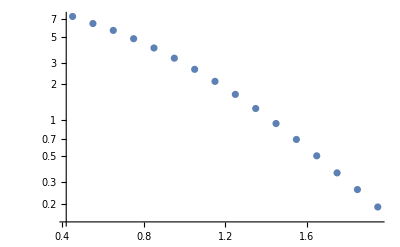

```mathematica
realplot=ListLogPlot[Table[{real[[2i-1]],real[[2i]]},{i,1,16}]]
```

reverse slope cT=38.4,T=0.249

C:\Users\86177\Desktop\大创\程序\Console4\Console4

%pt           TTT           TTS           TSS           TSS2j           SSS           SSS2j           Tot
        0.450    7.58085E+00    1.74943E-13    5.50353E-15    1.76745E-16    2.69138E-17    4.81975E-18    7.58085E+00
        0.550    7.25126E+00    3.72227E-14    1.19964E-15    3.72874E-17    2.57505E-17    1.02045E-18    7.25126E+00
        0.650    6.45816E+00    1.01657E-14    3.49024E-16    1.00789E-17    2.45355E-17    2.77004E-19    6.45816E+00
        0.750    5.46786E+00    3.33910E-15    1.30926E-16    3.25136E-18    2.33144E-17    8.97816E-20    5.46786E+00
        0.850    4.45937E+00    1.27201E-15    6.22411E-17    1.19799E-18    2.21197E-17    3.32485E-20    4.45937E+00
        0.950    3.53468E+00    5.50358E-16    3.62413E-17    4.89728E-19    2.09731E-17    1.36641E-20    3.53468E+00
        1.050    2.74014E+00    2.66840E-16    2.44915E-17    2.17653E-19    1.98870E-17    6.10642E-21    2.74014E+00
        1.150    2.08699E+00    1.43304E-16    1.82157E-17    1.03632E-19    1.88675E-17    2.92401E-21    2.08699E+00
        1.250    1.56700E+00    8.41530E-17    1.43493E-17    5.22803E-20    1.79166E-17    1.48368E-21    1.56700E+00
        1.350    1.16288E+00    5.32515E-17    1.16961E-17    2.77072E-20    1.70329E-17    7.90962E-22    1.16288E+00
        1.450    8.54630E-01    3.57714E-17    9.73569E-18    1.53226E-20    1.62136E-17    4.40039E-22    8.54630E-01
        1.550    6.22984E-01    2.51628E-17    8.21590E-18    8.79433E-21    1.54549E-17    2.54089E-22    6.22984E-01
        1.650    4.50989E-01    1.83278E-17    7.00082E-18    5.21530E-21    1.47525E-17    1.51604E-22    4.50989E-01
        1.750    3.24544E-01    1.37037E-17    6.00949E-18    3.18395E-21    1.41020E-17    9.31242E-23    3.24544E-01
        1.850    2.32354E-01    1.04515E-17    5.18937E-18    1.99492E-21    1.34991E-17    5.87085E-23    2.32354E-01
        1.950    1.65608E-01    8.09420E-18    4.50402E-18    1.27945E-21    1.29398E-17    3.78869E-23    1.65608E-01

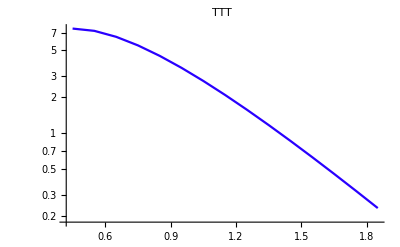
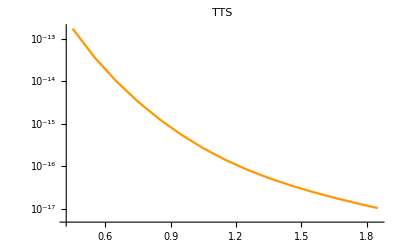
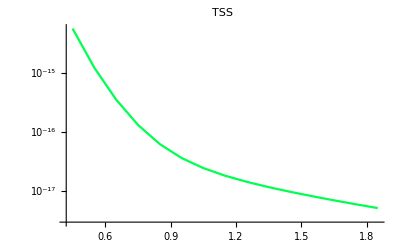
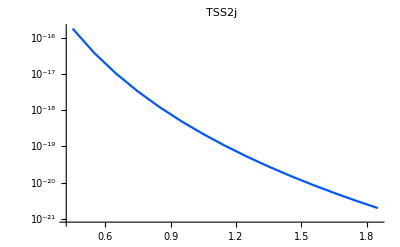
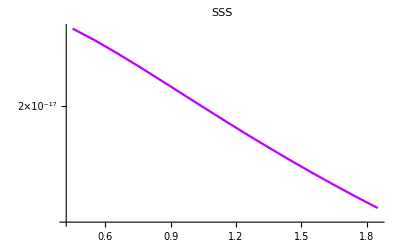
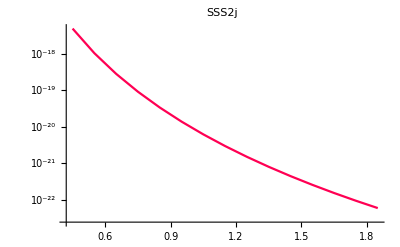
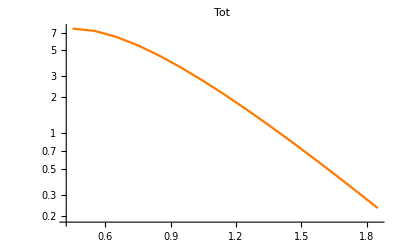

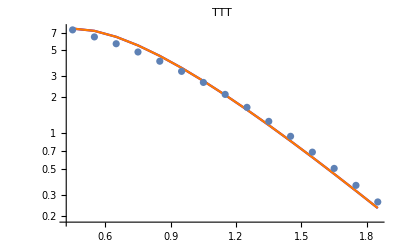

```mathematica
SetDirectory["C:\\Users\\86177\\Desktop\\大创\\程序\\Console4\\Console4"]
Import["C:\\Users\\86177\\Desktop\\大创\\程序\\Console4\\Console4\\dNptdpt_AuAu396_p_c025(2).txt"]
datalabel=StringSplit[StringTrim[StringSplit[%,"\n"][[1]]]];
datalist=StringReplace[#,"E"->"*10^"]&/@ StringSplit[#,"    "]&/@StringSplit[%%,"\n"][[2;;16]]//ToExpression;
Table[ListLogPlot[Join[Partition[datalist[[All,1]],1],Partition[datalist[[All,i]],1],2],PlotLabel->Style[datalabel[[i]],Hue[N@Log[i]]],Joined->True,PlotStyle->Hue[Log@i],PlotRange->Full],{i,2,8}]
Show[{%,realplot}]
```

%pt            TT            TS            SS            SS2j            Tot
        0.500    2.48907E+01    1.49108E+00    2.11733E-01    1.67315E-03    2.65952E+01
        0.800    1.15336E+01    4.80300E-01    5.09246E-02    4.31833E-04    1.20652E+01
        1.100    5.34431E+00    1.87198E-01    1.77224E-02    1.56652E-04    5.54939E+00
        1.400    2.47639E+00    8.06920E-02    7.35068E-03    6.69846E-05    2.56450E+00
        1.700    1.14748E+00    3.70315E-02    3.36667E-03    3.14488E-05    1.18791E+00
        2.000    5.31708E-01    1.77282E-02    1.64074E-03    1.56442E-05    5.51093E-01
        2.300    2.46377E-01    8.74248E-03    8.33865E-04    8.08144E-06    2.55962E-01
        2.600    1.14164E-01    4.40381E-03    4.36643E-04    4.28327E-06    1.19008E-01
        2.900    5.29000E-02    2.25307E-03    2.33505E-04    2.31265E-06    5.53889E-02
        3.200    2.45122E-02    1.16669E-03    1.27185E-04    1.26739E-06    2.58074E-02
        3.500    1.13582E-02    6.10608E-04    7.11397E-05    7.04044E-07    1.20407E-02
        3.800    5.26305E-03    3.23043E-04    4.08352E-05    3.96201E-07    5.62732E-03
        4.100    2.43874E-03    1.72938E-04    2.40503E-05    2.25829E-07    2.63595E-03
        4.400    1.13004E-03    9.38203E-05    1.45269E-05    1.30394E-07    1.23851E-03
        4.700    5.23624E-04    5.16660E-05    8.98997E-06    7.62962E-08    5.84356E-04
        5.000    2.42631E-04    2.89290E-05    5.69181E-06    4.52588E-08    2.77297E-04
        5.300    1.12428E-04    1.64940E-05    3.68062E-06    2.72295E-08    1.32630E-04
        5.600    5.20956E-05    9.58710E-06    2.42675E-06    1.66208E-08    6.41261E-05
        5.900    2.41395E-05    5.68518E-06    1.62870E-06    1.02949E-08    3.14637E-05
        6.200    1.11855E-05    3.44058E-06    1.11096E-06    6.47060E-09    1.57435E-05
        6.500    5.18303E-06    2.12469E-06    7.69113E-07    4.12625E-09    8.08095E-06
        6.800    2.40166E-06    1.33816E-06    5.39705E-07    2.66879E-09    4.28219E-06
        7.100    1.11285E-06    8.58824E-07    3.83440E-07    1.74996E-09    2.35687E-06
        7.400    5.15662E-07    5.61078E-07    2.75522E-07    1.16268E-09    1.35342E-06
        7.700    2.38942E-07    3.72684E-07    2.00041E-07    7.82254E-10    8.12450E-07
        8.000    1.10718E-07    2.51361E-07    1.46625E-07    5.32589E-10    5.09236E-07
        8.300    5.13035E-08    1.71931E-07    1.08411E-07    3.66701E-10    3.32012E-07
        8.600    2.37725E-08    1.19120E-07    8.07973E-08    2.55161E-10    2.23945E-07
        8.900    1.10154E-08    8.34946E-08    6.06571E-08    1.79296E-10    1.55346E-07
        9.200    5.10422E-09    5.91481E-08    4.58405E-08    1.27153E-10    1.10220E-07
        9.500    2.36514E-09    4.22997E-08    3.48530E-08    9.09354E-11    7.96088E-08
        9.800    1.09593E-09    3.05161E-08    2.66446E-08    6.55524E-11    5.83222E-08
       10.100    5.07822E-10    2.21835E-08    2.04703E-08    4.75898E-11    4.32091E-08
       10.400    2.35309E-10    1.62390E-08    1.57965E-08    3.47773E-11    3.23056E-08
       10.700    1.09035E-10    1.19639E-08    1.22378E-08    2.55713E-11    2.43363E-08
       11.000    5.05235E-11    8.86098E-09    9.51363E-09    1.88998E-11    1.84440E-08
       11.300    2.34110E-11    6.59680E-09    7.41794E-09    1.40405E-11    1.40522E-08
       11.600    1.08480E-11    4.93050E-09    5.79847E-09    1.04722E-11    1.07503E-08
       11.900    5.02661E-12    3.69846E-09    4.54187E-09    7.83990E-12    8.25320E-09
       12.200    2.32918E-12    2.78377E-09    3.56324E-09    5.89002E-12    6.35524E-09
       12.500    1.07927E-12    2.09965E-09    2.79858E-09    4.43528E-12    4.90375E-09
       12.800    5.00100E-13    1.58736E-09    2.19937E-09    3.34827E-12    3.79058E-09
       13.100    2.31731E-13    1.20114E-09    1.72864E-09    2.53071E-12    2.93254E-09
       13.400    1.07377E-13    9.09539E-10    1.35807E-09    1.91473E-12    2.26963E-09
       13.700    4.97553E-14    6.89200E-10    1.06586E-09    1.45009E-12    1.75656E-09

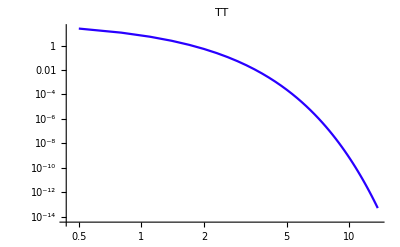
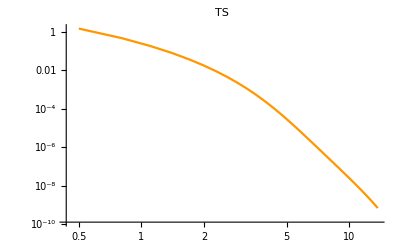
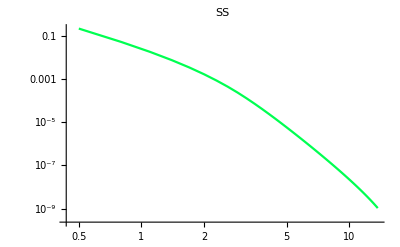
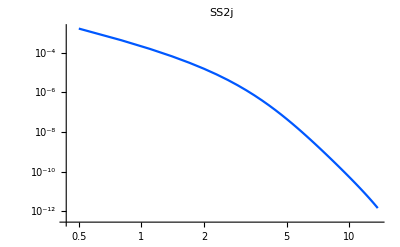
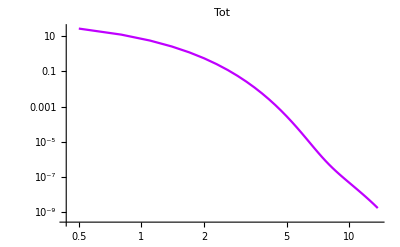

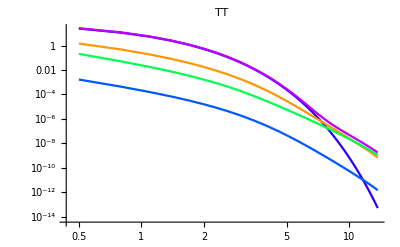

```mathematica
Import["D:\\大创\\prog2\\result\\dNptdpt_AuAu   _pion1_c025.txt"]
datalabel=StringSplit[StringTrim[StringSplit[%,"\n"][[1]]]];
datalist=StringReplace[#,"E"->"*10^"]&/@ StringSplit[#,"    "]&/@StringSplit[%%,"\n"][[2;;46]]//ToExpression;
Table[ListLogLogPlot[Join[Partition[datalist[[All,1]],1],Partition[datalist[[All,i]],1],2],PlotLabel->Style[datalabel[[i]],Hue[N@Log[i]]],Joined->True,PlotStyle->Hue[Log@i],PlotRange->Full],{i,2,6}]
Show@%
```

```mathematica
0.35*(39*10^-3)^0.105
```

0.24896